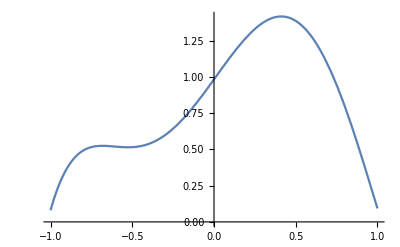

```mathematica
functionAfterSwap[t_] = 0.4(0.2+25(0.4t+0.4)-200(0.4t+0.4)^2+675(0.4t+0.4)^3 - 900(0.4t+0.4)^4+400(0.4t+0.4)^5);
Plot[functionAfterSwap[t], {t,-1,1}]
```

```mathematica
gauss2Nodes = f[-1/Sqrt[3]]+f[1/Sqrt[3]]

1.8225777777777772
```

```mathematica
gaussNodes = 5/9*f[-√(3/5)]+8/9 f[0]+5/9(f[√(3/5)])
1.6405333333333276
```

```mathematica
trapezoid = Abs[f[-1]+f[1]]
0.17279999999999407
```

```mathematica
rectangle = 2*f[0]
1.9647999999999968
```

```mathematica
simpson = Abs[1/3*(f[1]+4*f[0]+f[1])]
1.3717333333333273
```

```mathematica
actualResult =Integrate[f[t], {t,-1,1}]
1.640533333333333
```

```mathematica
Solve[{Integrate[1*(x^2+b*x+c), {x,0,1}]==0, Integrate[(x+2/3)*(x^2+b*x+c),{x,0,1}]==0} {b,c}]
```

Solve[{b (∫_0^1 (c+b (0.4+0.4 t)+(0.4+0.4 t)^2)ⅆ(0.4+0.4 t)==0),c (∫_0^1 (c+b (0.4+0.4 t)+(0.4+0.4 t)^2) (1.06667+0.4 t)ⅆ(0.4+0.4 t)==0)}]